## Highly Optimized Tolerance (HOT). Forest-fire model Problem 14.14

```mathematica
Clear["Global`*"];
```

```mathematica
counts[m_]:=#/.ComponentMeasurements[#,"Count"]&@MorphologicalComponents[m,CornerNeighbors->False]
```

```mathematica
SeedRandom[0];g=RandomVariate[BernoulliDistribution[0.4],{10,10}]; gcount=counts[g];  
{Image[g,ImageSize->Small],MatrixForm[gcount]}
```

{-Graphics-,(9 | 9 | 9 | 0 | 5 | 5 | 0 | 1 | 0 | 1
0 | 9 | 9 | 9 | 0 | 5 | 5 | 0 | 0 | 0
9 | 9 | 9 | 0 | 0 | 0 | 5 | 0 | 6 | 0
0 | 0 | 0 | 0 | 3 | 3 | 0 | 6 | 6 | 6
4 | 4 | 0 | 0 | 0 | 3 | 0 | 6 | 0 | 0
4 | 4 | 0 | 1 | 0 | 0 | 0 | 6 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 3 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 3 | 3 | 0
0 | 0 | 3 | 3 | 3 | 0 | 1 | 0 | 0 | 1)}

```mathematica
pmat[N_]:=Module[{mi,σi,mj,σj,temp,Z},mi=1; σi=0.4; mj=0.5; σj=0.2;temp=Table[(2^(-(mi+i/N)/σi^2))(2^(-(mj+j/N)/σj^2)),{i,N},{j,N}]; Z=Total[temp,2]; temp/Z]
```

```mathematica
yield[ρ_,N_]:=Module[{g,gcount,p,y},g=RandomVariate[BernoulliDistribution[ρ],{N,N}]; gcount=counts[g];p=pmat[N]; y=p*gcount; (Total[g,2]-Total[y,2])/N^2]  (* yield = trees-burned *)
```

```mathematica
SeedRandom[1];ytable=Table[yield[ρ,32],{ρ,0,1,0.05},{10}]//Transpose;(* 10 reps *)
```

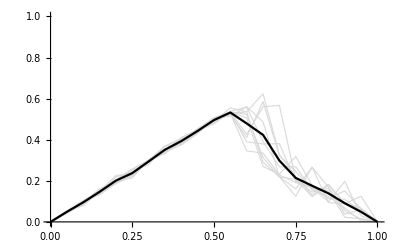

```mathematica
plot1=ListPlot[{Mean[ytable]},Joined->True,DataRange->{0,1},PlotRange->{0,1},PlotStyle->{Black,Thick}];
plot2=ListPlot[ytable,Joined->True,DataRange->{0,1},PlotRange->{0,1},PlotStyle->{{LightGray,Thickness[0.002]}}];Show[plot2,plot1]
```

Now look at evolved case.

```mathematica
evolved[n_,d_,ρmax_]:=Module[{k,i,p,gd,gd1,gdlist,nlist,pos,d1,dbest},
p=pmat[n]; gd=ConstantArray[0,{n,n}]; gdlist=Position[gd,0]; k=1;
yd=ConstantArray[0,n^2];
While[k≤ n^2,
nlist=Length[gdlist];d1=Min[d,nlist];
i=RandomSample[Range[nlist],d1]; (* d different elements *)
pos=gdlist[[i]]; (* gets d random elements of gdlist *)
gd1=MapAt[1&,gd,#]&/@pos;  (* d forests w/ 1 new tree from pos *)
ydlist=Table[(Total[gd1[[l]],2]-Total[counts[gd1[[l]]]*p,2])/n^2 ,{l,d1}];
yd[[k]]=Max[ydlist];  (* maximum yield over the d1 possibilities *)
dbest=Position[ydlist,Max[ydlist]][[1,1]];
gd=gd1[[dbest]];   (* best of the d *)
gdlist=Delete[gdlist,i[[dbest]]];
If[k==Round[ρmax n^2],gdmax=gd];
k++]; ]
```

```mathematica
SeedRandom[3];evolved[32,32,0.9]//Timing
```

{987.191,Null}

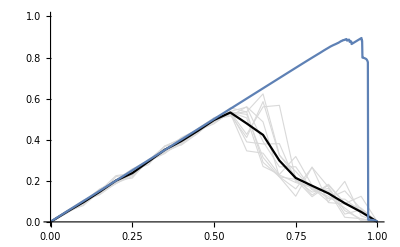

```mathematica
ydall=yd;plot3=ListPlot[ydall,Joined->True,DataRange->{0,1},PlotRange->{0,1}];
Show[plot2,plot1,plot3]
```

Images of Sample lattices near peak yield

```mathematica
SeedRandom[8];
grandom=RandomVariate[BernoulliDistribution[0.6],{32,32}];
```

```mathematica
GraphicsRow[{Image[grandom,ImageSize->Small],Image[gdmax,ImageSize->Small]},200]
```

-Graphics-

Export data

```mathematica
(* 
SetDirectory[NotebookDirectory[]];
Export["HOTydall.dat",ydall];
Export["HOTytable.dat",ytableᵀ];
*)
```